```mathematica
μ=0;σ=1;
P[x_]=1/(σ √(2π))Exp[-(x-μ)^2/(2 σ^2)];
```

```mathematica
NN=100000;
a=-5;b=5;
dist=Table[0,{NN}];
dist[[1]]=RandomReal[{a,b}];
For[i=2,i≤NN,i++,
move=RandomReal[{a,b}];
myrand=RandomReal[{0,1}];
If[P[move]/P[dist[[i-1]]]≥myrand,dist[[i]]=move,dist[[i]]=dist[[i-1]];
]
]
```

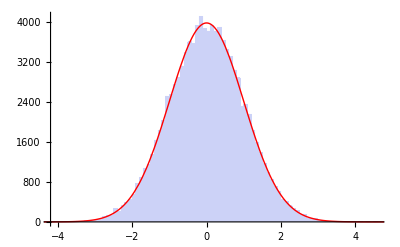

```mathematica
A=10000;
p1=Histogram[dist];
p2=Plot[A*P[x],{x,-10,10},PlotRange->All,PlotStyle->{Thick,Red}];
Show[p1,p2]
```

```mathematica
(*Same but for LaTeX*)
```

```mathematica
mu=0;sig=1;
P[x_]=1/(sig*Sqrt[2 Pi])*Exp[-((x-mu)^2/(2*sig^2))];
num=100000;
a=-5;b=5;
dist=Table[0,{num}];
dist[[1]]=RandomReal[{a,b}];
For[i=2,i≤num,i++,move=RandomReal[{a,b}];
myrand=RandomReal[{0,1}];
If[P[move]/P[dist[[i-1]]]≥myrand,dist[[i]]=move,dist[[i]]=dist[[i-1]];]]
A=10000;
p1=Histogram[dist];
p2=Plot[A*P[x],{x,-10,10},PlotRange->All,PlotStyle->{Thick,Red}];
Show[p1,p2]
```